# Monetary Policy

## Setup

Set working directory

```mathematica
SetDirectory["/Users/nicoloceneda/Dropbox/Bhamra-Ceneda/theory/macroeconomics/code"];
```

## Consumption and Investment

## Maximum Safe to Spend

Clear variables

```mathematica
Clear["Global`*"]
```

Maximum safe to spend

```mathematica
maxC[μ_,T_]:=(μ *w0)/((1+μ)-(1+μ)^(1-T))
```

Maximum safe to spend when μ = 0

```mathematica
Limit[(w0*μ)/((1+μ)-(1+μ)^(1-T)),μ->0]
```

w0/T

Household wealth

```mathematica
w[μ_,t_,T_]:=w0*(1+μ)^t-maxC[μ,T]*(1+μ)*((1+μ)^t-1)/μ
```

Parameters

```mathematica
w0=1;
```

Plot household maximum safe to spend and wealth

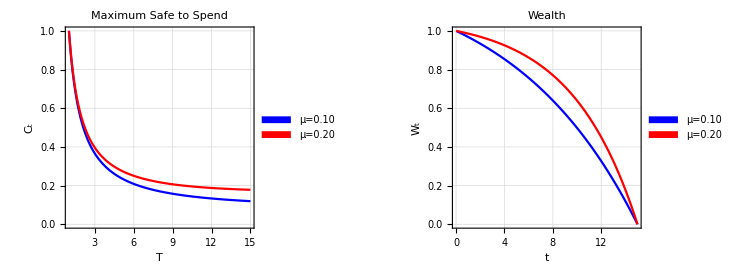

```mathematica
householdConsumption= Plot[{maxC[0.10,T],maxC[0.20,T]},{T,1,15},
PlotStyle->{Blue,Red},
PlotLabel->"Maximum Safe to Spend",
PlotLegends->Placed[SwatchLegend[{"μ=0.10","μ=0.20"}],{0.87,0.88}],
FrameLabel->{"T","C_t"},
Frame->True,
GridLines->Automatic,
PlotRange->{{1,15},{0,1}}];
householdWealth= Plot[{w[0.10,t,15],w[0.20,t,15]},{t,0.01,15},
PlotStyle->{Blue,Red},
PlotLabel->"Wealth",
PlotLegends->Placed[SwatchLegend[{"μ=0.10","μ=0.20"}],{0.87,0.88}],
FrameLabel->{"t","W_t"},
Frame->True,
GridLines->Automatic,
PlotRange->{{0,15},{0,1}}];
householdWealth=GraphicsGrid[{{householdConsumption,householdWealth}},ImageSize->{750,270}]
Export["images/household-wealth.jpeg",householdWealth];
```

## Static Optimal Control Problem in Discrete Time

Household utility

```mathematica
u[c_,η_]:=(c^(1-η)-1)/(1-η)
```

Plot household utility

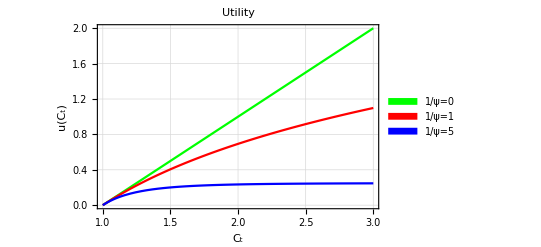

```mathematica
householdUtility=Plot[{u[c,0],Log[c],u[c,5]},{c,1,3},
PlotStyle->{Green,Red,Blue},
PlotLabel->"Utility",
PlotLegends->Placed[SwatchLegend[{"1/ψ=0","1/ψ=1","1/ψ=5"}],{0.12,0.75}],
FrameLabel->{"C_t","u(C_t)"},
Frame->True,
GridLines->Automatic,
PlotRange->{{1,3},{0,2}}]
Export["images/household-utility.jpeg",householdUtility];
```

Clear variables

```mathematica
Clear["Global`*"]
```

Optimal consumption-wealth ratio

```mathematica
optimalCW[β_,ψ_,μ_]:=(1+μ)^(1-ψ)/((1+μ)^(1-ψ)+β^ψ)
```

Plot optimal savings-wealth ratio and consumption-wealth ratio

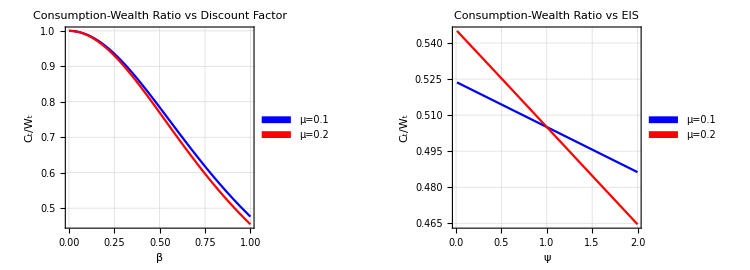

```mathematica
consumptionWealthBeta=Plot[{optimalCW[β,2,0.1],optimalCW[β,2,0.2]},{β,0,1},
PlotStyle->{Blue,Red},
PlotLabel->"Consumption-Wealth Ratio vs Discount Factor",
PlotLegends->Placed[SwatchLegend[{"μ=0.1","μ=0.2"}],{0.87,0.88}],
FrameLabel->{"β","C_t/W_t"},
Frame->True,
GridLines->Automatic,
PlotRange->{{0,1},{Min[optimalCW[1,2,0.1],optimalCW[1,2,0.2]],1}}];
consumptionWealthPsi=Plot[{optimalCW[0.98,ψ,0.1],optimalCW[0.98,ψ,0.2]},{ψ,0.01,2},
PlotStyle->{Blue,Red},
PlotLabel->"Consumption-Wealth Ratio vs EIS",
PlotLegends->Placed[SwatchLegend[{"μ=0.1","μ=0.2"}],{0.87,0.88}],
FrameLabel->{"ψ","C_t/W_t"},
Frame->True,
GridLines->Automatic,
PlotRange->{{0,2},{Min[optimalCW[0.98,0.01,0.2],optimalCW[0.98,2,0.2]],Max[optimalCW[0.98,0.01,0.2],optimalCW[0.98,2,0.2]]}}];
ConsumptionWealthRatio=GraphicsGrid[{{consumptionWealthBeta,consumptionWealthPsi}},ImageSize->{750,270}]
Export["images/consumption-wealth-ratio-discrete-static.jpeg",ConsumptionWealthRatio];
```

## Dynamic Optimal Control Problem in Discrete Time

Clear variables

```mathematica
Clear["Global`*"]
```

Optimal consumption - wealth ratio

```mathematica
optimalCW[μ_,t_]:=(1-β^ψ(1/(1+μ))^(1-ψ))/(1-(β^ψ(1/(1+μ))^(1-ψ))^(T-t+1))
```

Parameters

```mathematica
β=0.98;
ψ=2;
T=15;
```

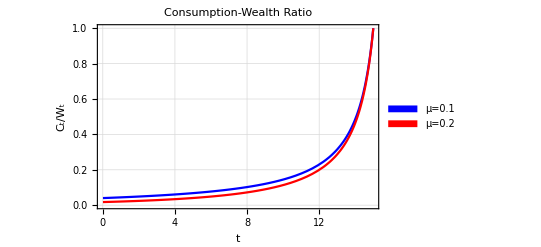

```mathematica
consumptionWealth=Plot[{optimalCW[0.1,t],optimalCW[0.2,t]},{t,0.01,15},
PlotStyle->{Blue,Red},
PlotLabel->"Consumption-Wealth Ratio",
PlotLegends->Placed[SwatchLegend[{"μ=0.1","μ=0.2"}],{0.12,0.88}],
FrameLabel->{"t","C_t/W_t"},
Frame->True,
GridLines->Automatic,
PlotRange->{{0,15},{0,Max[optimalCW[0.1,15],optimalCW[0.2,15]]}}]
Export["images/consumption-wealth-ratio-discrete-dynamic.jpeg",consumptionWealth];
```

## Pontryagin' s maximum principle

Functionals

```mathematica
yCoordinate[x_]:=√(1-x^2)
vector=Graphics3D[{Red,Arrow[{{0.7,-yCoordinate[0.7],0},{0,0,0}}]},Axes->True,Boxed->True];
sphere=SphericalPlot3D[1,{θ,0,π/2},{ϕ,0,2 π},
ImageSize->Medium,
PlotStyle->{Directive[Blue,Specularity[White,1]],Opacity[0.4]}];
vectorSphere=Show[vector,sphere,AxesLabel->{"x","y","z"}]
Export["images/sphere.jpeg",vectorSphere];
```

-Graphics3D-

## Dynamic Optimal Control Problem in Continuous Time

Clear variables

```mathematica
Clear["Global`*"]
```

Optimal consumption - wealth ratio

```mathematica
optimalCW[δ_,ψ_,μ_]:=ψ*δ+(1-ψ)*μ
```

Boundary conditions

```mathematica
Solve[ψ*δ+(1-ψ)*μ==0,δ]
```

{{δ→(μ (-1+ψ))/ψ}}

```mathematica
boundaryDelta[ψ_,μ_]:=(μ (-1+ψ))/ψ
```

```mathematica
Max[boundaryDelta[2,0.1],boundaryDelta[2,0.2]]
```

0.1

```mathematica
Solve[ψ*δ+(1-ψ)*μ==0,ψ]
```

{{ψ→-μ/(δ-μ)}}

```mathematica
boundaryPsi[δ_,μ_]:=-μ/(δ-μ)
```

```mathematica
Min[boundaryPsi[0.05,0.1],boundaryPsi[0.05,0.2]]
```

1.33333

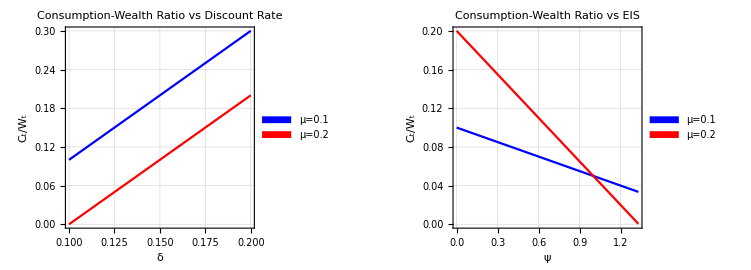

```mathematica
consumptionWealthBeta=Plot[{optimalCW[δ,2,0.1],optimalCW[δ,2,0.2]},{δ,0.1,0.2},
PlotStyle->{Blue,Red},
PlotLabel->"Consumption-Wealth Ratio vs Discount Rate",
PlotLegends->Placed[SwatchLegend[{"μ=0.1","μ=0.2"}],{0.12,0.88}],
FrameLabel->{"δ","C_t/W_t"},
Frame->True,
GridLines->Automatic,
PlotRange->{{0.1,0.2},{0,0.3}}];
consumptionWealthPsi=Plot[{optimalCW[0.05,ψ,0.1],optimalCW[0.05,ψ,0.2]},{ψ,0,1.33},
PlotStyle->{Blue,Red},
PlotLabel->"Consumption-Wealth Ratio vs EIS",
PlotLegends->Placed[SwatchLegend[{"μ=0.1","μ=0.2"}],{0.87,0.88}],
FrameLabel->{"ψ","C_t/W_t"},
Frame->True,
GridLines->Automatic,
PlotRange->{{0,1.33},{0,0.2}}];
ConsumptionWealthRatio=GraphicsGrid[{{consumptionWealthBeta,consumptionWealthPsi}},ImageSize->{751,270}]
Export["images/consumption-wealth-ratio-continuous-dynamic.jpeg",ConsumptionWealthRatio];
```

## Solow Growth Model

Clear variables

```mathematica
Clear["Global`*"]
```

Production function

```mathematica
y[k_,l_]:=k^α*l^(1-α)
```

Parameters

```mathematica
α=0.5;
```

Plot production function

```mathematica
productionFunction=Plot3D[y[k,l],{k,0,1},{l,0,1},AxesLabel->{Subscript[K, t],Subscript[L, t],Subscript[Y, t]},ImageSize->Medium,PlotStyle->Directive[Blue,Specularity[White,1]],ViewPoint->{-5, -5, 3}]
Export["images/production-function.jpeg",productionFunction];
```

-Graphics3D-